```mathematica
CellPrint[Cell["Directory","Section"]]
CellPrint[Cell["Main code & XZ independent noise:","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"general_codes.nb"],Appearance->"DialogBox"]
CellPrint[Cell["Depoloarizing Noise:","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"depolarizing_noise.nb"],Appearance->"DialogBox"]
CellPrint[Cell["XZ uneven Noise:","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"xz_uneven_noise.nb"],Appearance->"DialogBox"]
CellPrint[Cell["Approxiating polynomials:","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"approximating_polynomials.nb"],Appearance->"DialogBox"]
CellPrint[Cell["Depolarizing noise with Measurement error :","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"depolarizing_noise_ME.nb"],Appearance->"DialogBox"]
CellPrint[Cell["XZ (symmetric) noise with Measurement error :","Text"]]
Hyperlink[StringJoin[NotebookDirectory[],"xz_noise_ME.nb"],Appearance->"DialogBox"]
SetDirectory[NotebookDirectory[]]
```

## Directory

Main code & XZ independent noise:

Depoloarizing Noise:

XZ uneven Noise:

Approxiating polynomials:

Depolarizing noise with Measurement error :

XZ (symmetric) noise with Measurement error :

/Users/naomi/Dropbox/&Projects/Small codes

## Small codes

```mathematica
Takes a set of stabilizer generators, returns the logical success rate as a function of physical error rate.
```

## Analysis Functions

```mathematica
getQPosition[{p_,n_}]:=If[p=="x",2*n-1,2*n]
(* returns the list position of qubit specified by pauli state p in {'x','z'} and its qubit number n *)
getQPositionComplement[{p_,n_}]:=If[p=="x",2*n,2*n-1]




createStabilizerLists[stabilizers_]:=Module[{s},
(* This function takes a set of stabilizers, expressed as lists of pauli operators
e.g. S = {{x1,x2,x3},{x4,x5,x6}}
and transforms them into list of position that they detect in measurement - that is the positions of the complementary basis. 
*)
s={StringTake[#,1],ToExpression@StringDrop[#,1]}&/@(SymbolName[#]&/@#)&/@stabilizers;
s = getQPositionComplement[#]&/@#&/@s;
s
]

createStabilizerVectors[stabilizers_,nqubits_]:=Module[{s,sv},
(* takes stabilizer lists ( of qubit positions), and transforms them to vectors of {+1,-1} entries to be used to 'apply' the stabilizer generators to the qubits *)

s={StringTake[#,1],ToExpression@StringDrop[#,1]}&/@(SymbolName[#]&/@#)&/@stabilizers;
s = getQPosition[#]&/@#&/@s;

sv= ConstantArray[1,{Length[s],nqubits*2}];
ReplacePart[sv⟦#⟧,-1,{#}&/@s⟦#⟧]&/@Range[Length[s]]
]



checkCodeDefinition[nQubits_,S_,L_,display_:False]:=Module[{sLists,sVecs,sGroup,lLists,lVecs,lGroup,a,b,c,d},

Print["Checking the code definition..."];
(* generate the stabilizer lists and qubit array *)
sLists = createStabilizerLists[S]; (* for measurement *)
sVecs = createStabilizerVectors[S,nQubits];(* for applying operators *)
sGroup =Times@@#&/@ Subsets[sVecs,All];

(* generate the logical operators *)
lLists = createStabilizerLists[L];
lVecs = createStabilizerVectors[L,nQubits];
lGroup=Times@@#&/@Subsets[lVecs,All];

(* check stabilizers are independent *)

If[Length[DeleteDuplicates[sGroup]]≠Length[sGroup],Print["PROBLEM: stabilizer generators not independent"]]

(* check logical operators not in the stabilizer group *)
If[Intersection[sGroup,lGroup]≠{1},Print["PROBLEM: logical operators in S"]];

(* check the logical operators commute with the stabilizer group *)
If[MemberQ[ checkCommute[#]&/@Tuples[{lVecs,sVecs}] ,False],Print["PROBLEM: a logical operator is anticommuting with a stabilizer generator"]];
If[display,
a=(checkCommute[#]&/@Tuples[{lVecs,sVecs}]);
b=Position[a,False];
Print["The following pairs of operators don't commute: "];
Print[labelFromQpos[#]&/@#&/@#&/@#&/@(Tuples[{lLists,sLists}][[#]]&/@b)];];

(* check the logical operators anticommute with one another *)
If[MemberQ[checkCommute[#]&/@Subsets[lVecs,{2,2}],True],Print["PROBLEM: a pair of the logical operators commute"]];


(* check the stabilizer generators commute *)
If[MemberQ[(checkCommute[#]&/@Subsets[sVecs,{2,2}]),False],Print["PROBLEM: The stabilizer generators don't all commute"]];
If[display,
a=(checkCommute[#]&/@Subsets[sVecs,{2,2}]);
b=Position[a,False];
Print["The following pairs of operators don't commute: "];
Print[labelFromQpos[#]&/@#&/@#&/@#&/@(Subsets[sLists,{2,2}][[#]]&/@b)];];


Print["all checks complete"]

]

labelFromQpos[q_]:=If[EvenQ[q],StringJoin[{"x",ToString[q/2]}],StringJoin[{"z",ToString[(q+1)/2]}]]






checkOperatorCommute[{a_,b_}]:=Module[{},
If[a=={1,1}||b=={1,1},Return[True];];
If[a==b,Return[True];,Return[False];];
]

checkCommute[{list1_,list2_}]:=Module[{opValues},
opValues = checkOperatorCommute[#]&/@(Thread@{Partition[list1,2],Partition[list2,2]});
If[EvenQ@Count[opValues,False],True,False]
]
nQubits = 7;
S={{x1,x2},{x1,x4,x3},{x4,x5,x6,x7},{z1,z2,z4,z5},{z3,z4,z6},{z5,z7}};
L={{x1,x4,x6},{z3,z4,z5}};
checkCodeDefinition[nQubits,S,L]

applyStabilizer[Q_,svec_]:=Q svec
(* apply the stabilizer operator svec to the qubit state Q *)


measureStabilizer[Q_,svec_]:=Times@@Part[Q,svec]
measureSyndrome[Q_,sLists_]:=measureStabilizer[Q,#]&/@sLists

Clear[generateSyndromes]
generateSyndromes[sLists_,sGroup_,nQubits_,testErrors_:4]:=Module[{Q,Qs,syndromes,Qstates,,syn,errorConfigs},
(* generate staring Qs for each syndrome *)
Q=ConstantArray[1,2*nQubits];
errorConfigs=Subsets[Range[2*nQubits],{0,testErrors}];
syndromes={};
Qstates = {};
For[i=1,i<Length[errorConfigs],i++,
Qs=ReplacePart[Q,-1,{#}&/@errorConfigs[[i]]];
syn=measureSyndrome[Qs,sLists];
If[!MemberQ[syndromes,syn],
syndromes=Append[syndromes,syn];
Qstates=Append[Qstates,Qs];
]
If[Length[syndromes]==Length[sGroup],Break[]];
];
If[Length[syndromes]≠Length[sGroup],Print["WARNING: Not all syndromes found"]];
{syndromes,Qstates}
]

countErrors[Q_]:=Count[Q,-1];
(* count the number of errors for a X,Z separate model. NOTE: change this function to account for a depolarizeing noise model *)

countSyndromeErrors[Qs_,lGroup_,sGroup_]:=Module[{errCount,QsL},
(* create logical variants *)
QsL=Qs #&/@lGroup;

(* count errors of each weight for each logical state *)
errCount={};
For[i=1,i≤Length[lGroup],i++,
errCount=Append[errCount,Tally[countErrors[QsL[[i]] # ]&/@ sGroup]]; ];

errCount
]


probFromErrorTally[pTally_,nQ_,p_]:=Plus@@(#[[2]]*((p)^#[[1]](1-p)^(2*nQ-#[[1]]))&/@pTally)

probSuccessFromTally[errCount_,nQ_,p_]:=Module[{probs},
probs=probFromErrorTally[#,nQ,p]&/@errCount;
(Max@probs)/Plus@@probs
];

checkCount[errCount_]:=Module[{tot},
For[i=1,i≤Length[errCount],i++,
tot=Plus@@(#[[2]]&/@errCount[[i]]);
Print[{tot," configurations counted"}];
];
]
countSyndromeErrors[Qs_,lGroup_,sGroup_,counter_]:=Module[{errCount,QsL},
(* counter is a function that takes Q as a parameter, and returns the number of errors
according to the relevant noise model *)

(* create logical variants *)
QsL=Qs #&/@lGroup;
(* count errors of each weight for each logical state *)
errCount={};
For[i=1,i≤Length[lGroup],i++,
errCount=Append[errCount,Tally[counter[QsL[[i]] # ]&/@ sGroup]]; ];
errCount
]


countSyndromeErrors[Qs_,lGroup_,sGroup_,counter_]:=Module[{errCount,QsL},
(* counter is a function that takes Q as a parameter, and returns the number of errors
according to the relevant noise model *)
(* create logical variants *)
QsL=(Qs #)&/@lGroup;
(* count errors of each weight for each logical state *)
errCount={};
For[i=1,i≤Length[lGroup],i++,
errCount=Append[errCount,Tally[counter[QsL[[i]] # ]&/@ sGroup]]; ];

errCount
]


Clear[testCode]
testCode[code_,testErrors_:5]:=Module[{nQubits,S,L,sLists,sVecs,sGroup,errCount,lLists,lGroup,lVecs,Qstates,syndromes},

(* specify the stabilizer generators, S (These should be independent operators) , and the Logical operators, L. *)

{nQubits,S,L}=code;
(* generate the stabilizer lists and qubit array *)
sLists = createStabilizerLists[S]; (* for measurement *)
sVecs = createStabilizerVectors[S,nQubits];(* for applying operators *)
sGroup =Times@@#&/@ Subsets[sVecs,All];

(* generate the logical operators *)
lLists = createStabilizerLists[L];
lVecs = createStabilizerVectors[L,nQubits];
lGroup=Times@@#&/@Subsets[lVecs,All];

{syndromes,Qstates}=generateSyndromes[sLists,sGroup,nQubits,testErrors];


errCount = countSyndromeErrors[#,lGroup,sGroup,countErrors]&/@Qstates;
{syndromes,errCount}

]


(*Plotting *)

plotResult[errCount_,color_:1,label_:None]:=Module[{totals,succRate,probs},
probs = probFromErrorTally[#,nQubits,p]&/@#&/@errCount;
totals=Plus@@#&/@probs;

succRate = Table[{p,Plus@@((probSuccessFromTally[#,nQubits,p]&/@errCount)(totals))},{p,0.001,0.1,0.001}];

Show[
ListPlot[succRate,Joined->True,PlotLegends->{label},PlotStyle->ColorData[97,color]],
Plot[(1-p)^2,{p,0,1},PlotStyle->Red]
]
]


pxpz[a_,p_]:=Module[{pzval,pxval,b},

(* return px and pz as a function of the overall single qubit error rate p when they are related
as px=a pz *)
If[a≤1,pzval = (1+a-√(1+2 a+a^2-4 a p))/(2 a);pxval = a pzval;,
b=1/a;pxval =(1+b-√(1+2 b+b^2-4 b p))/(2 b);pzval= b pxval;];
{pxval,pzval}
]

polynomialXZ[tally_,nQ_]:=(#[[2]]*(1-px)^(2*nQ-#[[1]])px^#[[1]]&/@#&/@#)&/@tally;

encodingPower[pVal_,polynomials_]:=Module[{poly},
successRate[pVal,polynomials]/(1-p)
]
successRate[pVal_,polynomials_]:=Module[{poly},
poly=polynomials/.{p->pVal};
Plus@@(Max[#]&/@poly)
]
plotResultsF[results_,nQ_,function_,color_:1,label_:None]:=Module[{polynomials,ep,pxVal,pzVal},
(*polynomials = (#[[2]]*(1-p)^(2*nQ-#[[1]])p^#[[1]]&/@#&/@#)&/@results;*)
polynomials=polynomialXZ[results,nQ];
polynomials=(Plus@@#&/@#)&/@polynomials;
{pxVal,pzVal}=pxpz[1,p];

ep=Table[{p,function[p,polynomials/.{px->pxVal}]},{p,0.001,0.2,0.001}];
ListPlot[ep,Joined->True,PlotStyle->ColorData[97,color],PlotLegends->{label}]
]

plotResultsFcolor[results_,nQ_,function_,color_:1,label_:None]:=Module[{polynomials,ep,pxVal,pzVal},
(*polynomials = (#[[2]]*(1-p)^(2*nQ-#[[1]])p^#[[1]]&/@#&/@#)&/@results;*)
polynomials=polynomialXZ[results,nQ];
polynomials=(Plus@@#&/@#)&/@polynomials;
{pxVal,pzVal}=pxpz[1,p];

ep=Table[{p,function[p,polynomials/.{px->pxVal}]},{p,0.001,0.2,0.001}];
ListPlot[ep,Joined->True,PlotStyle->{ColorData[97,color],Thickness[0.01],Dotted},PlotLegends->{label}]
]

checkResultsValid[results_,nQ_]:=Module[{polynomials},
polynomials = (#[[2]]*(1-p)^(2*nQ-#[[1]])p^#[[1]]&/@#&/@#)&/@results;
polynomials=(Plus@@#&/@#)&/@polynomials;
FullSimplify[Plus@@Plus@@polynomials]
]

plotDataF[results_,nQ_,function_]:=Module[{polynomials,ep,pxVal,pzVal},
(*polynomials = (#[[2]]*(1-p)^(2*nQ-#[[1]])p^#[[1]]&/@#&/@#)&/@results;*)
polynomials=polynomialXZ[results,nQ];
polynomials=(Plus@@#&/@#)&/@polynomials;
{pxVal,pzVal}=pxpz[1,p];

ep=Table[{p,function[p,polynomials/.{px->pxVal}]},{p,0.001,0.2,0.001}]
]

truncatePolynomials[results_,nmax_]:=Select[#,#[[1]]≤nmax&]&/@#&/@results
```

Checking the code definition...

all checks complete

Checking the code definition...

all checks complete

Checking the code definition...

all checks complete

all checks complete

## Surface Codes

## Generate polynomials

```mathematica
testCode[codeT5]>>"data/polyXZT5.txt"
```

```mathematica
testCode[codeP5]>>"data/planar5.txt"
```

```mathematica
testCode[codeP6]>>"data/planar6.txt"
```

```mathematica
testCode[codeP7]>> "data/planar7a.txt"
```

```mathematica
testCode[codeP7b]>> "data/planar7b.txt"
```

```mathematica
testCode[codeP8]>> "data/planar8.txt"
```

```mathematica
testCode[codeP8b]>> "data/planar8b.txt"
```

```mathematica
testCode[codeP9]>> "data/planar9.txt"
```

```mathematica
testCode[codeP10]>> "data/planar10.txt"
```

```mathematica
testCode[codeP11,6]>>"data/planar11.txt"
```

```mathematica
testCode[codeP12,6]>>"data/planar12.txt"
```

```mathematica
testCode[codeP13]>>"data/planar13.txt"
```

```mathematica
testCode[codeC7]>> "data/color7.txt"
```

```mathematica
testCode[codeC9]>> "data/colorC9.txt"
```

```mathematica
testCode[codeC11]>> "data/colorC11.txt"
```

## Generate plot data

```mathematica
{syndromesT5,polyT5}=<<"data/polyXZT5.txt";
checkResultsValid[polyT5,5]
plotDataF[polyT5,5,successRate]>>"data/XZT5"
```

```mathematica
{syndromesP5,polyP5}=<<"data/planar5.txt";
checkResultsValid[polyP5,5]
plotDataF[polyP5,5,successRate]>>"data/XZP5"
```

```mathematica
{syndromesP6,polyP6}=<<"data/planar6.txt";
checkResultsValid[polyP6,6]
plotDataF[polyP6,6,successRate]>>"data/XZP6"
```

```mathematica
{syndromesP7a,polyP7a}=<<"data/planar7a.txt";
checkResultsValid[polyP7a,7];
plotDataF[polyP7a,7,successRate]>>"data/XZP7"
```

```mathematica
{syndromesP7b,polyP7b}=<<"data/planar7b.txt";
checkResultsValid[polyP7b,7];
plotDataF[polyP7b,7,successRate]>>"data/XZP7b"
```

```mathematica
{syndromesP8,polyP8}=<<"data/planar8.txt";
checkResultsValid[polyP8,8]
plotDataF[polyP8,8,successRate]>>"data/XZP8"
```

```mathematica
{syndromesP8b,polyP8b}=<<"data/planar8b.txt";
checkResultsValid[polyP8b,8]
```

```mathematica
{syndromesP9,polyP9}=<<"data/planar9.txt";
checkResultsValid[polyP9,9];
plotDataF[polyP9,9,successRate]>>"data/XZP9"
```

```mathematica
{syndromesP10,polyP10}=<<"data/planar10.txt";
checkResultsValid[polyP10,10];
```

```mathematica
{syndromesP11,polyP11}=<<"data/planar11.txt";
checkResultsValid[polyP11,11]
```

```mathematica
{syndromesP13,polyP13}=<<"data/planar13.txt";
plotDataF[truncatePolynomials[polyP13,7],13,successRate]>>"data/XZP13"
```

```mathematica
{syndromesC7,polyC7}=<<"data/color7.txt";
checkResultsValid[polyC7,7]
plotDataF[polyC7,7,successRate]>>"data/XZC7"
```

```mathematica
{syndromesC9,polyC9}=<<"data/colorC9.txt";
checkResultsValid[polyC9,9]
plotDataF[polyC9,9,successRate]>>"data/XZC9"
```

```mathematica
{syndromesC11,polyC11}=<<"data/color11.txt";
checkResultsValid[polyC11,11]
plotDataF[polyC11,11,successRate]>>"data/XZC11"
```

```mathematica
pGCCXZ[p_,a_]:=Module[{px,pz,nx,nz,e1x,e1z},
{px,pz}=pxpz[a,p];
nx=(1-px)^15;
nz=(1-pz)^15;
e1x=15*(1-px)^14*px;
e1z=15*(1-pz)^14*pz;
(nx+e1x)(nz+e1z)
]

Table[{p,pGCCXZ[p,1]},{p,0.0001,0.15,0.0001}]>>"data/XZGCC15";
```

## Summary Plots - surface codes

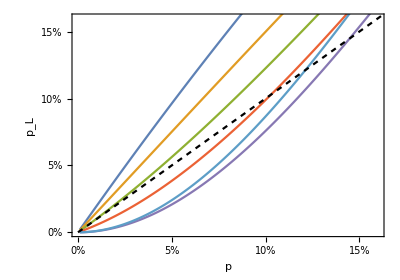

```mathematica
dataXZT5=<<"data/XZT5";
dataXZP5=<<"data/XZP5";
dataXZP6=<<"data/XZP6";
dataXZP7=<<"data/XZP7";
dataXZP7b=<<"data/XZP7b";
dataXZP8=<<"data/XZP8";
dataXZP9=<<"data/XZP9";

dataXZP13=<<"data/XZP13";



pLog[data_]:={#[[1]],1-#[[2]]}&/@data;

Show[ListPlot[pLog@#[[1]],Joined->True,PlotStyle->ColorData[97,#[[2]]]]&/@

{{dataXZP5,1},{dataXZP6,2},{dataXZP7,3},{dataXZP8,4},{dataXZP9,5},{dataXZP13,7}},

Plot[p,{p,0,1},PlotStyle->Directive[Black,Dashing[0.01]]],

Frame->True,
PlotRange->{{0,0.16},{0,0.16}},
FrameLabel->{"p","p_L"},
LabelStyle->15,
FrameTicks->{{{0,"0%"},{0.05,"5%"},{0.1,"10%"},{0.15,"15%"}},{{0,"0%"},{0.05,"5%"},{0.1,"10%"},{0.15,"15%"},{0.2,"20%"}},{},{}},
AspectRatio->0.7


]
```

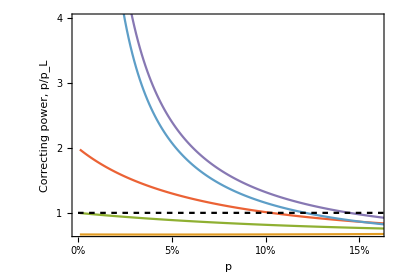

```mathematica
cp[data_]:={#[[1]],#[[1]]/(1-#[[2]])}&/@data

Show[ListPlot[cp@#[[1]],Joined->True,PlotStyle->ColorData[97,#[[2]]]]&/@

{{dataXZP5,1},{dataXZP6,2},{dataXZP7,3},{dataXZP8,4},{dataXZP9,5},{dataXZP13,7}},

Plot[1,{p,0,1},PlotStyle->Directive[Black,Dashing[0.01]]],

Frame->True,
PlotRange->{{0,0.16},{0.7,4}},
FrameLabel->{"p","Correcting power, p/p_L"},
LabelStyle->15,
FrameTicks->{{{0,"0%"},{0.05,"5%"},{0.1,"10%"},{0.15,"15%"}},{1,2,3,4},{},{}},
AspectRatio->0.7


]
```

## Summary Plots - color codes

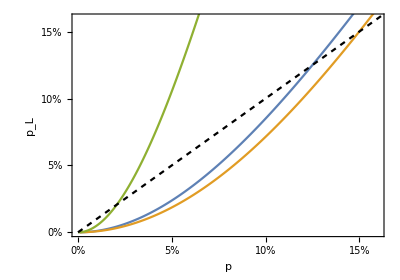

```mathematica
dataXZC7=<<"data/XZC7";
dataXZC9=<<"data/XZC9";
dataXZC11=<<"data/XZC11";

dataXZGCC15=<<"data/XZGCC15";

pLog[data_]:={#[[1]],1-#[[2]]}&/@data;

Show[ListPlot[pLog@#[[1]],Joined->True,PlotStyle->ColorData[97,#[[2]]]]&/@

{{dataXZC7,1},{dataXZC11,2},{dataXZGCC15,3}},

Plot[p,{p,0,1},PlotStyle->Directive[Black,Dashing[0.01]]],

Frame->True,
PlotRange->{{0,0.16},{0,0.16}},
FrameLabel->{"p","p_L"},
LabelStyle->15,
FrameTicks->{{{0,"0%"},{0.05,"5%"},{0.1,"10%"},{0.15,"15%"}},{{0,"0%"},{0.05,"5%"},{0.1,"10%"},{0.15,"15%"},{0.2,"20%"}},{},{}},
AspectRatio->0.7


]
```

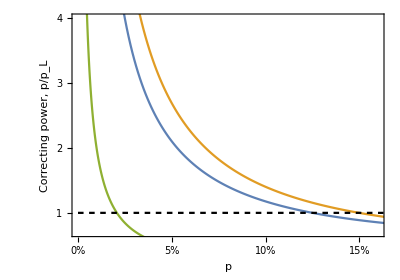

```mathematica
cp[data_]:={#[[1]],#[[1]]/(1-#[[2]])}&/@data

Show[ListPlot[cp@#[[1]],Joined->True,PlotStyle->ColorData[97,#[[2]]]]&/@

{{dataXZC7,1},{dataXZC11,2},{dataXZGCC15,3}},

Plot[1,{p,0,1},PlotStyle->Directive[Black,Dashing[0.01]]],

Frame->True,
PlotRange->{{0,0.16},{0.7,4}},
FrameLabel->{"p","Correcting power, p/p_L"},
LabelStyle->15,
FrameTicks->{{{0,"0%"},{0.05,"5%"},{0.1,"10%"},{0.15,"15%"}},{1,2,3,4},{},{}},
AspectRatio->0.7


]
```

## 6 qubit Planar Code

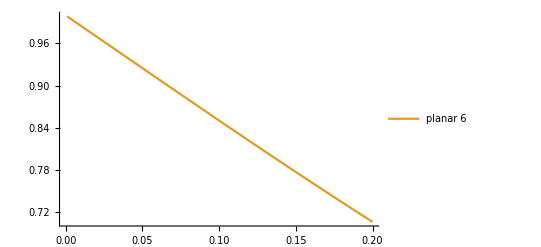
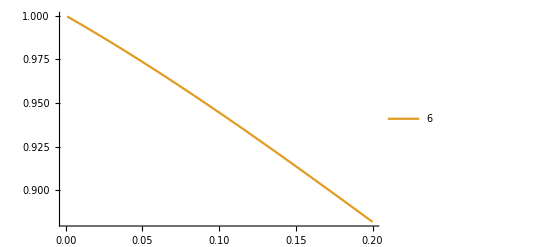

```mathematica
{plotPlanar6,epPlanar6} ={ plotResultsF[polyP6,6,successRate,2,"planar 6"],plotResultsF[polyP6,6,encodingPower,2,"6"]}
```

## 7 qubit Planar Codes

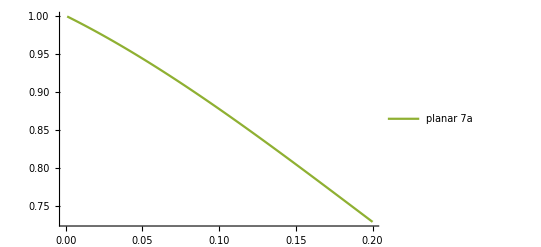
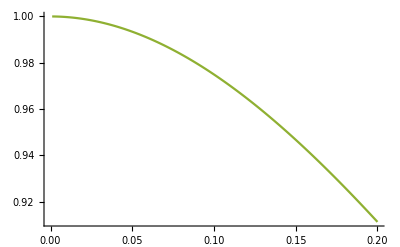

```mathematica
{plotPlanar7a ,epPlanar7a}={plotResultsF[polyP7a,7,successRate,3,"planar 7a"],plotResultsF[polyP7a,7,encodingPower,3]}
```

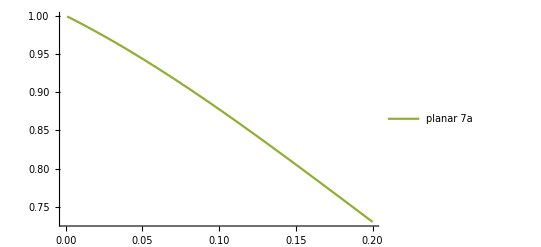
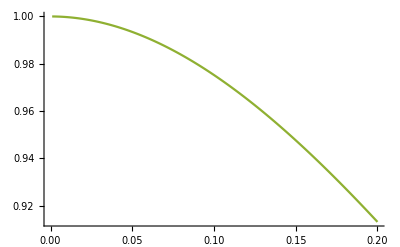

```mathematica
{plotPlanar7b ,epPlanar7b}={plotResultsF[polyP7b,7,successRate,3,"planar 7a"],plotResultsF[polyP7b,7,encodingPower,3]}
```

## 8 qubit surface Code

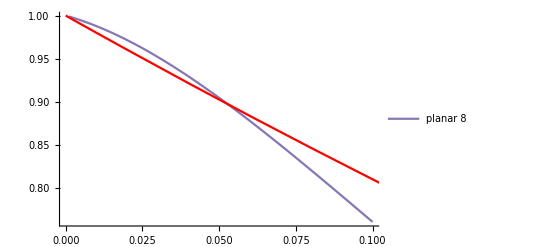

```mathematica
plotPlanar8=plotResultsF[polyP8,8,successRate,4,"planar 8"];
{plotResult[polyP8,5,"planar 8"]}
```

1

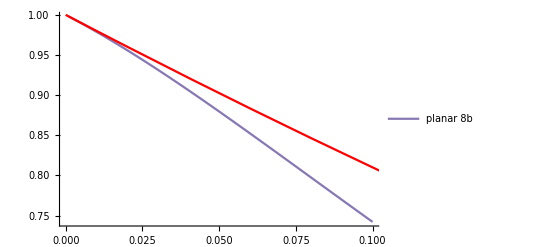

```mathematica
plotPlanar8=plotResultsF[polyP8b,8,successRate,4,"planar 8"];
{plotResult[polyP8b,5,"planar 8b"]}
```

## 9 qubit surface Code

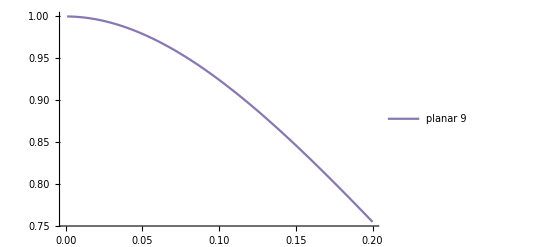

```mathematica
plotPlanar9=plotResultsF[truncatePolynomials[polyP9,5],9,successRate,5,"planar 9"];
{plotPlanar9}
```

## 10 qubit surface Code

```mathematica
plotPlanar10=plotResultsF[polyP10,10,successRate,10,"planar 10"];
```

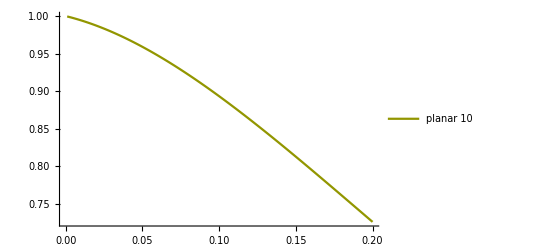

```mathematica
{plotPlanar10}
```

## 11 qubit surface Code

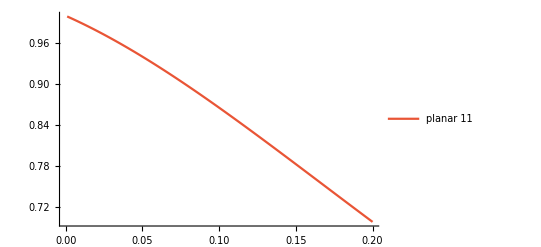

```mathematica
plotPlanar11=plotResultsF[polyP11,11,successRate,11,"planar 11"]
```

## 12 qubit surface Code

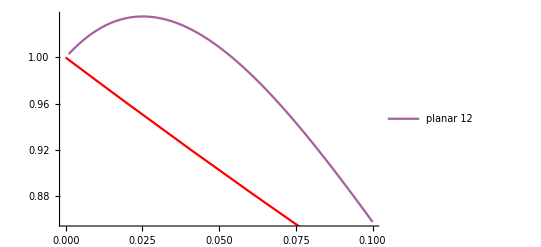

```mathematica
{successRate
plotPlanar12=plotResultF[planar12,12,successRate,12"planar 12"]
```

## 13 qubit surface Code

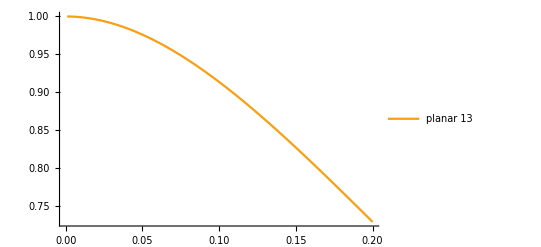

```mathematica
{syndromesP13,polyP13}=<<"data/planar13.txt";
plotPlanar13=plotResultsF[truncatePolynomials[polyP13,7],13,successRate,13,"planar 13"];
```

## Color Codes

## 7 qubit Color Code

1

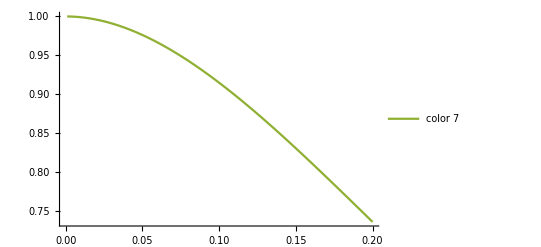
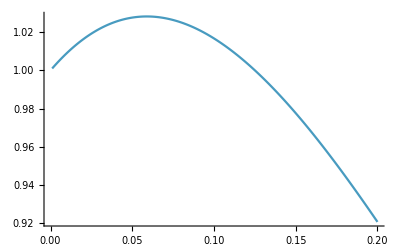

```mathematica
{plotColor7,epColor7}={plotResultsF[polyC7,7,successRate,3,"color 7"],plotResultsF[polyC7,7,encodingPower,20]}
```

## 9 qubit Color Code

1

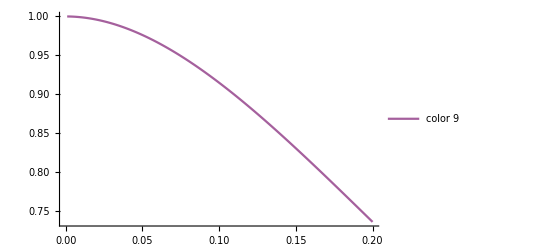

```mathematica
{plotColor9}={plotResultsF[polyC9,9,successRate,9,"color 9"]}
```

## 11 qubit Color Code

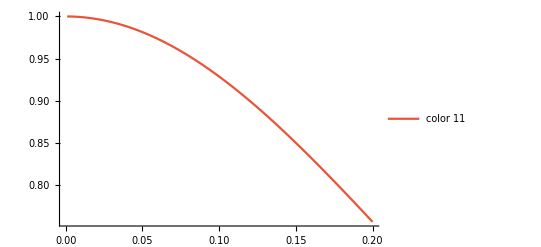

```mathematica
{plotColor11} = {plotResultsF[polyC11,11,successRate,11,"color 11"]}
```

```mathematica
testCode[codeC11b]>>"data/colorC11b.txt"

(* Problem with this code *)
```

```mathematica
{syndromesC11b,polyC11b}=<<"data/color11b.txt";
checkResultsValid[polyC11b,11];
plotColor11b=plotResultsF[polyC11b,11,encodingPower,12,"color11b"]
```

## 15 qubit Gauge Color Code

```mathematica
nQubits = 15;
S={{x1,x2,x3,x5,x7,x8,x9,x12},{x1,x2,x3,x4,x6,x7,x10,x13},{x1,x2,x4,x5,x6,x8,x11,x14},{x1,x3,x4,x5,x11,x9,x10,x15},{z1,z2,z3,z5,z7,z8,z9,z12},{z1,z2,z3,z4,z6,z7,z10,z13},{z1,z2,z4,z5,z6,z8,z11,z14},{z1,z3,z4,z5,z11,z9,z10,z15}};
L={{x1,x2,x3,x4,x5},{z1,z2,z3,z4,z5}};
checkCodeDefinition[nQubits,S,L]
gcc15=testCode[S,L,nQubits];
gcc15>>"data/gcc15.txt"
```

Checking the code definition...

all checks complete

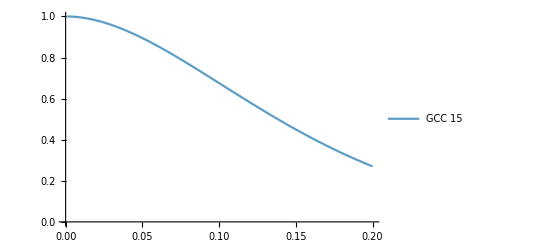

```mathematica
{syndromesGCC15,polyGCC15}=<<"data/gcc15.txt";
plotGCC15=plotResultsF[gcc15,15,successRate,7,"GCC 15"]
```

## Summary plots

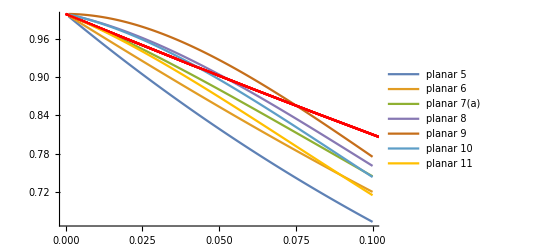

```mathematica
Show[plotPlanar5,plotPlanar6,plotPlanar7a,plotPlanar8,plotPlanar9,plotPlanar10,plotPlanar11]
```

```mathematica
Planar Codes
```

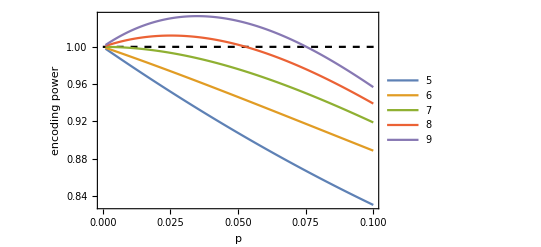

```mathematica
Show[epPlanar5,ListPlot[{{0,1},{1,1}},Joined->True,PlotStyle->{Black,Dashed}],
epPlanar6,epPlanar7,epPlanar8,epPlanar9,PlotRange->{{0,0.1},All},Frame->True,FrameLabel->{"p","encoding power"},LabelStyle->Medium]
```

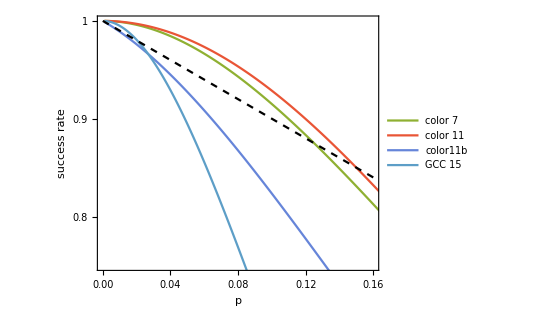

```mathematica
Show[plotColor7,plotColor11,plotColor11b,plotGCC15,
Plot[(1-p),{p,0,1},PlotStyle->{Black,Dashed}],

PlotRange->{{0,0.16},{0.75,1}},Frame->True,FrameLabel->{"p","success rate"},LabelStyle->20,FrameTicks->{{{0.8,0.9,1},None},{Automatic,None}},AspectRatio->0.8]
```

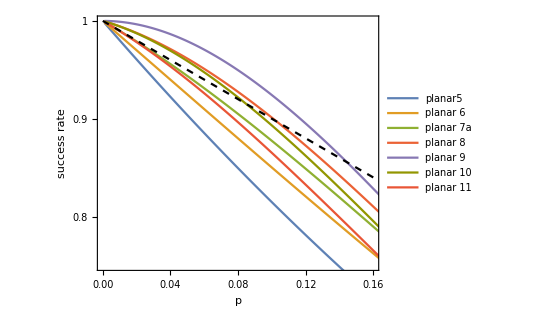

```mathematica
Show[plotPlanar5,plotPlanar6,plotPlanar7a,plotPlanar8,plotPlanar9,plotPlanar10,plotPlanar11,
Plot[(1-p),{p,0,1},PlotStyle->{Black,Dashed}],

PlotRange->{{0,0.16},{0.75,1}},Frame->True,FrameLabel->{"p","success rate"},LabelStyle->20,FrameTicks->{{{0.8,0.9,1},None},{Automatic,None}},AspectRatio->0.8]
```

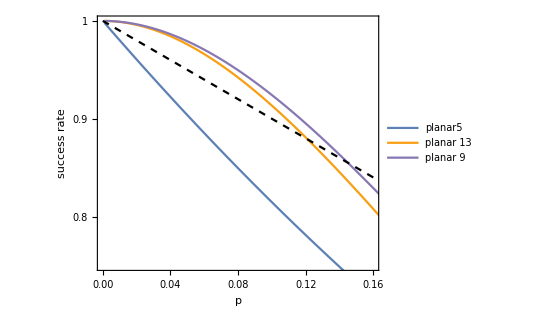

```mathematica
Show[plotPlanar5,plotPlanar13,plotPlanar9,
Plot[(1-p),{p,0,1},PlotStyle->{Black,Dashed}],
PlotRange->{{0,0.16},{0.75,1}},Frame->True,FrameLabel->{"p","success rate"},LabelStyle->20,FrameTicks->{{{0.8,0.9,1},None},{Automatic,None}},AspectRatio->0.8]
```